### Start by defining the van der Pol oscillator and finding its steady states:

```mathematica
vars={x,v};
vanderpol[μ_]:={v,μ (1-x^2) v-x};

(*Find the steady state.*)

eqns = vanderpol[μ]=={0,0};
steadyStates = Solve[eqns,vars]//Flatten;
Labeled[steadyStates,"Steady states of the van der Pol oscillator. More on this later."]
```

{x→0,v→0}Steady states of the van der Pol oscillator. More on this later.

### Compute the Jacobian at the fixed point. From its eigenvalues, determine the nature of the fixed point.

```mathematica
Print["The Jacobian."]
jacobian = D[vanderpol[μ],{vars}];
jacobian/.steadyStates
Print["Eigenvalues of the Jacobian at the stationary point x = v = 0."]
Eigenvalues[%%]
```

The Jacobian.

{{0,1},{-1,μ}}

Eigenvalues of the Jacobian at the stationary point x = v = 0.

{1/2 (μ-√(-4+μ^2)),1/2 (μ+√(-4+μ^2))}

#### Let’s consider the system with zero velocity and find the region in the μ-x plane where the Eigenvalues are complex-valued.

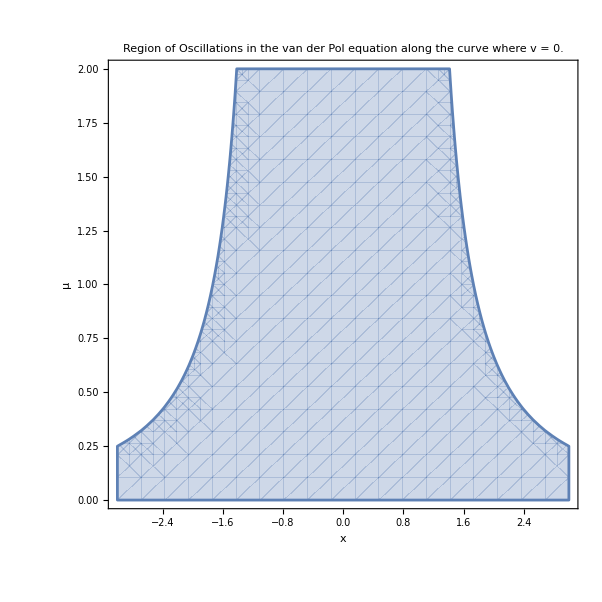

```mathematica
eigenvalues[x_,v_,μ_] = Eigenvalues[jacobian];
(*Plot the region of oscilatory behavior in the x-μ plane.*)
stability[x_,μ_]=eigenvalues[x,0,μ];

RegionPlot[Im[eigenvalues[x,0,μ][[1]]]!=0,{x,-3,3},{μ,0,2},FrameLabel->{"x","μ"},PlotLabel->"Region of Oscillations in the van der Pol equation along the curve where v = 0."]
```

### Note that there is no region of unstable growth, where the eigenvalues have a positive real part.

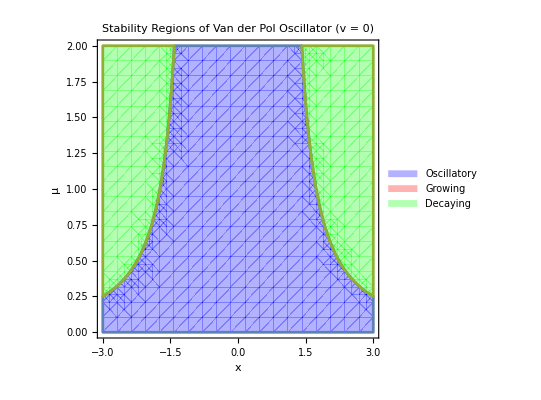

```mathematica
RegionPlot[{(*Oscillatory region:complex eigenvalues*)Im[eigenvalues[x,0,μ][[1]]]!=0,(*Growth region:real part>0*)Re[eigenvalues[x,0,μ][[1]]]>0&&Im[eigenvalues[x,0,μ][[1]]]==0,(*Decay region:real part<0*)Re[eigenvalues[x,0,μ][[1]]]<0&&Im[eigenvalues[x,0,μ][[1]]]==0},{x,-3,3},{μ,0,2},FrameLabel->{"x","μ"},PlotLabel->"Stability Regions of Van der Pol Oscillator (v = 0)",PlotStyle->{{Blue,Opacity[0.3]},(*Oscillatory*){Red,Opacity[0.3]},(*Growing*){Green,Opacity[0.3]}    (*Decaying*)},PlotLegends->{"Oscillatory","Growing","Decaying"}]
```

### The steady-states in this system are nontrivial; indeed the point at x = v = 0 is trivial! To open our minds a bit, consider the curves of zero velocity and zero acceleration. These are the so-called nullclines of the equation. I’ll plot them in blue and red, and alongside, i’ll visualize the forcing function f(x,v) for μ = 1. I’ll even do you one better! I’ll plot the vector field corresponding to the direction of flow to a local solution.

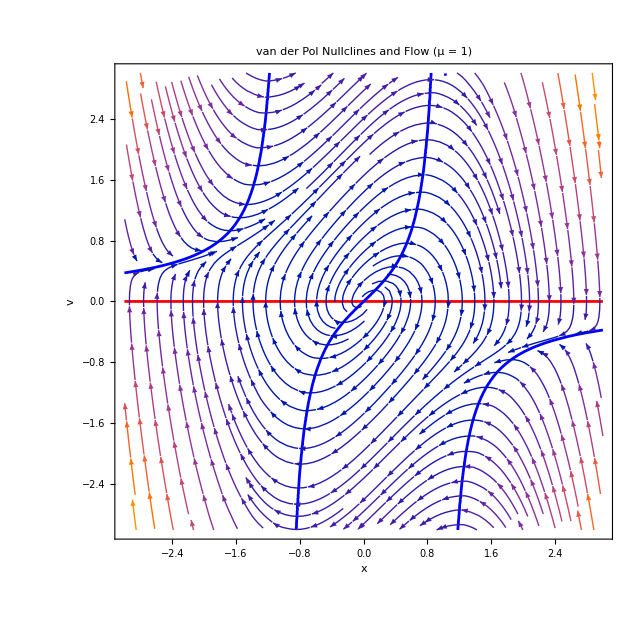

```mathematica
Module[{vwin = 3,xwin=3},
Show[ContourPlot[{v==0,v==x/(1*(1-x^2))},{x,-xwin,xwin},{v,-vwin,vwin},ContourStyle->{Red,Blue}],(*Direction field*)StreamPlot[vanderpol[1],{x,-xwin,xwin},{v,-vwin,vwin},StreamPoints->Fine],FrameLabel->{"x","v"},PlotLabel->"van der Pol Nullclines and Flow (μ = 1)"]
]
```